```mathematica
With[
{min=6,max=11},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[max],{1<->2,2<->3,3<->1,4<-> 5,5<->6,6<->4},VertexLabels->"Name"]},
PadLeft[
Map[Last,FormulaSummary2[FindFullFormula[g,Table[{j},{j,1,max}]]]],
max+1]
]
,
{kk,Range[min,max]}],
kk],
TableHeadings->{Range[min,max],Range[min,max+1]}
]
]
```

$Aborted

```mathematica
With[
{min=6,max=18},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[kk],{1<->2,2<->3,3<->1,4<-> 5,5<->6,6<->4},VertexLabels->"Name"]},
PadRight[Rest[Rest[CompleteBaseCoeff[ChromaticPolynomial[g,x]]]],max]

]
,
{kk,Range[min,max]}],
kk],
TableHeadings->{Range[min,max],Range[0,max]},
TableDepth->2
]
]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
6 | 0 | 6 | 18 | 9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 18 | 78 | 63 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 54 | 330 | 393 | 153 | 22 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 162 | 1374 | 2295 | 1311 | 307 | 30 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 486 | 5658 | 12849 | 10161 | 3460 | 547 | 39 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 0 | 1458 | 23118 | 69903 | 73815 | 34381 | 7836 | 898 | 49 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 0 | 4374 | 93930 | 372633 | 512793 | 314482 | 97069 | 15918 | 1388 | 60 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13 | 0 | 13122 | 380094 | 1957095 | 3449391 | 2714167 | 1091034 | 240331 | 29798 | 2048 | 72 | 1 | 0 | 0 | 0 | 0 | 0 | 0
14 | 0 | 39366 | 1533498 | 10165569 | 22653441 | 22448560 | 11442439 | 3254013 | 538311 | 52326 | 2912 | 85 | 1 | 0 | 0 | 0 | 0 | 0
15 | 0 | 118098 | 6173358 | 52361343 | 146086215 | 179793361 | 113988072 | 40728556 | 8637123 | 1113897 | 87270 | 4017 | 99 | 1 | 0 | 0 | 0 | 0
16 | 0 | 354294 | 24811530 | 267980073 | 928878633 | 1404639742 | 1091697937 | 480545076 | 127099786 | 20889990 | 2161137 | 139491 | 5403 | 114 | 1 | 0 | 0 | 0
17 | 0 | 1062882 | 99600414 | 1364711895 | 5841251871 | 10761356827 | 10138223238 | 5416603621 | 1751542936 | 356889676 | 46823634 | 3974520 | 215133 | 7113 | 130 | 1 | 0 | 0
18 | 0 | 3188646 | 399464538 | 6923159889 | 36412223121 | 81170749660 | 91867142731 | 58887655827 | 22932032981 | 5677329372 | 918773284 | 98492394 | 6986382 | 321828 | 9193 | 147 | 1 | 0

```mathematica
Select[Keys[allGraphs6],IsomorphicGraphQ[allGraphs6[#,"graph"],Graph[{1<->2,2<->3,3<->1,4<-> 5,5<->6,6<->4}]]&]
```

{6396988,5321080,4962576,4843080,2128924,1778844,1662156,729036,612444,262684}

```mathematica
FormulaSummary2[FindFullFormula[allGraphs6[6396988,"graph"],Table[{j},{j,1,6}]]]
```

{{3,6},{4,18},{5,9},{6,1}}

```mathematica
Table[StirlingS2[6,6-k],{k,0,6}]
```

{1,15,65,90,31,1,0}

```mathematica
allGraphs6[6396988,"graph"]
```

-Graphics-

```mathematica
allGraphs6[6396988,"colofour"]
```

v14x25x36+v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x35x6+v14x2x36x5+v14x2x3x5x6+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x34x6+v15x2x36x4+v15x2x3x4x6+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x34x5+v16x2x35x4+v16x2x3x4x5+v1x24x35x6+v1x24x36x5+v1x24x3x5x6+v1x25x34x6+v1x25x36x4+v1x25x3x4x6+v1x26x34x5+v1x26x35x4+v1x26x3x4x5+v1x2x34x5x6+v1x2x35x4x6+v1x2x36x4x5+v1x2x3x4x5x6

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[allGraphs6[6396988,"graph"],x]]
```

{0,0,0,6,18,9,1}

```mathematica
StirlingS2[6,5]
```

15

```mathematica
With[
{min=6,max=18},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[kk],{1<->2,2<->3,3<->1,4<-> 5,5<->6,6<->4},VertexLabels->"Name"]},
MatrixForm[{
PadRight[Table[
StirlingS2[kk,kk-mm]
,{mm,0,kk}
],max]
,
PadRight[Reverse[Rest[CompleteBaseCoeff[ChromaticPolynomial[g,x]]]],max],
PadRight[Table[
StirlingS2[kk,kk-mm]
,{mm,0,kk}
],max]-PadRight[Reverse[Rest[CompleteBaseCoeff[ChromaticPolynomial[g,x]]]],max]
}]

]
,
{kk,Range[min,max]}],
kk],
TableHeadings->{Range[min,max],Range[0,max]},
TableDepth->2
]
]
```

6 | (1 | 15 | 65 | 90 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 9 | 18 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 47 | 84 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
7 | (1 | 21 | 140 | 350 | 301 | 63 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 15 | 63 | 78 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 77 | 272 | 283 | 63 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
8 | (1 | 28 | 266 | 1050 | 1701 | 966 | 127 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 22 | 153 | 393 | 330 | 54 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 113 | 657 | 1371 | 912 | 127 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
9 | (1 | 36 | 462 | 2646 | 6951 | 7770 | 3025 | 255 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 30 | 307 | 1311 | 2295 | 1374 | 162 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 155 | 1335 | 4656 | 6396 | 2863 | 255 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
10 | (1 | 45 | 750 | 5880 | 22827 | 42525 | 34105 | 9330 | 511 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 39 | 547 | 3460 | 10161 | 12849 | 5658 | 486 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 203 | 2420 | 12666 | 29676 | 28447 | 8844 | 511 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
11 | (1 | 55 | 1155 | 11880 | 63987 | 179487 | 246730 | 145750 | 28501 | 1023 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 49 | 898 | 7836 | 34381 | 73815 | 69903 | 23118 | 1458 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 257 | 4044 | 29606 | 105672 | 176827 | 122632 | 27043 | 1023 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
12 | (1 | 66 | 1705 | 22275 | 159027 | 627396 | 1323652 | 1379400 | 611501 | 86526 | 2047 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 60 | 1388 | 15918 | 97069 | 314482 | 512793 | 372633 | 93930 | 4374 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 317 | 6357 | 61958 | 312914 | 810859 | 1006767 | 517571 | 82152 | 2047 | 1 | 0 | 0 | 0 | 0 | 0 | 0)
13 | (1 | 78 | 2431 | 39325 | 359502 | 1899612 | 5715424 | 9321312 | 7508501 | 2532530 | 261625 | 4095 | 1 | 0 | 0 | 0 | 0 | 0
1 | 72 | 2048 | 29798 | 240331 | 1091034 | 2714167 | 3449391 | 1957095 | 380094 | 13122 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 383 | 9527 | 119171 | 808578 | 3001257 | 5871921 | 5551406 | 2152436 | 248503 | 4095 | 1 | 0 | 0 | 0 | 0 | 0)
14 | (1 | 91 | 3367 | 66066 | 752752 | 5135130 | 20912320 | 49329280 | 63436373 | 40075035 | 10391745 | 788970 | 8191 | 1 | 0 | 0 | 0 | 0
1 | 85 | 2912 | 52326 | 538311 | 3254013 | 11442439 | 22448560 | 22653441 | 10165569 | 1533498 | 39366 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 455 | 13740 | 214441 | 1881117 | 9469881 | 26880720 | 40782932 | 29909466 | 8858247 | 749604 | 8191 | 1 | 0 | 0 | 0 | 0)
15 | (1 | 105 | 4550 | 106470 | 1479478 | 12662650 | 67128490 | 216627840 | 408741333 | 420693273 | 210766920 | 42355950 | 2375101 | 16383 | 1 | 0 | 0 | 0
1 | 99 | 4017 | 87270 | 1113897 | 8637123 | 40728556 | 113988072 | 179793361 | 146086215 | 52361343 | 6173358 | 118098 | 0 | 0 | 0 | 0 | 0
0 | 6 | 533 | 19200 | 365581 | 4025527 | 26399934 | 102639768 | 228947972 | 274607058 | 158405577 | 36182592 | 2257003 | 16383 | 1 | 0 | 0 | 0)
16 | (1 | 120 | 6020 | 165620 | 2757118 | 28936908 | 193754990 | 820784250 | 2141764053 | 3281882604 | 2734926558 | 1096190550 | 171798901 | 7141686 | 32767 | 1 | 0 | 0
1 | 114 | 5403 | 139491 | 2161137 | 20889990 | 127099786 | 480545076 | 1091697937 | 1404639742 | 928878633 | 267980073 | 24811530 | 354294 | 0 | 0 | 0 | 0
0 | 6 | 617 | 26129 | 595981 | 8046918 | 66655204 | 340239174 | 1050066116 | 1877242862 | 1806047925 | 828210477 | 146987371 | 6787392 | 32767 | 1 | 0 | 0)
17 | (1 | 136 | 7820 | 249900 | 4910178 | 62022324 | 512060978 | 2758334150 | 9528822303 | 20415995028 | 25708104786 | 17505749898 | 5652751651 | 694337290 | 21457825 | 65535 | 1 | 0
1 | 130 | 7113 | 215133 | 3974520 | 46823634 | 356889676 | 1751542936 | 5416603621 | 10138223238 | 10761356827 | 5841251871 | 1364711895 | 99600414 | 1062882 | 0 | 0 | 0
0 | 6 | 707 | 34767 | 935658 | 15198690 | 155171302 | 1006791214 | 4112218682 | 10277771790 | 14946747959 | 11664498027 | 4288039756 | 594736876 | 20394943 | 65535 | 1 | 0)
18 | (1 | 153 | 9996 | 367200 | 8408778 | 125854638 | 1256328866 | 8391004908 | 37112163803 | 106175395755 | 189036065010 | 197462483400 | 110687251039 | 28958095545 | 2798806985 | 64439010 | 131071 | 1
1 | 147 | 9193 | 321828 | 6986382 | 98492394 | 918773284 | 5677329372 | 22932032981 | 58887655827 | 91867142731 | 81170749660 | 36412223121 | 6923159889 | 399464538 | 3188646 | 0 | 0
0 | 6 | 803 | 45372 | 1422396 | 27362244 | 337555582 | 2713675536 | 14180130822 | 47287739928 | 97168922279 | 116291733740 | 74275027918 | 22034935656 | 2399342447 | 61250364 | 131071 | 1)

```mathematica
With[
{min=6,max=18},
TableForm[
Monitor[
Table[PadRight[
Table[
StirlingS2[kk,kk-mm]
,{mm,0,kk}
],max]
,
{kk,Range[min,max]}],
kk],
TableHeadings->{Range[min,max],Range[1,max]},
TableDepth->2
]
]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
6 | 1 | 15 | 65 | 90 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 1 | 21 | 140 | 350 | 301 | 63 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 1 | 28 | 266 | 1050 | 1701 | 966 | 127 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 1 | 36 | 462 | 2646 | 6951 | 7770 | 3025 | 255 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 45 | 750 | 5880 | 22827 | 42525 | 34105 | 9330 | 511 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 1 | 55 | 1155 | 11880 | 63987 | 179487 | 246730 | 145750 | 28501 | 1023 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 1 | 66 | 1705 | 22275 | 159027 | 627396 | 1323652 | 1379400 | 611501 | 86526 | 2047 | 1 | 0 | 0 | 0 | 0 | 0 | 0
13 | 1 | 78 | 2431 | 39325 | 359502 | 1899612 | 5715424 | 9321312 | 7508501 | 2532530 | 261625 | 4095 | 1 | 0 | 0 | 0 | 0 | 0
14 | 1 | 91 | 3367 | 66066 | 752752 | 5135130 | 20912320 | 49329280 | 63436373 | 40075035 | 10391745 | 788970 | 8191 | 1 | 0 | 0 | 0 | 0
15 | 1 | 105 | 4550 | 106470 | 1479478 | 12662650 | 67128490 | 216627840 | 408741333 | 420693273 | 210766920 | 42355950 | 2375101 | 16383 | 1 | 0 | 0 | 0
16 | 1 | 120 | 6020 | 165620 | 2757118 | 28936908 | 193754990 | 820784250 | 2141764053 | 3281882604 | 2734926558 | 1096190550 | 171798901 | 7141686 | 32767 | 1 | 0 | 0
17 | 1 | 136 | 7820 | 249900 | 4910178 | 62022324 | 512060978 | 2758334150 | 9528822303 | 20415995028 | 25708104786 | 17505749898 | 5652751651 | 694337290 | 21457825 | 65535 | 1 | 0
18 | 1 | 153 | 9996 | 367200 | 8408778 | 125854638 | 1256328866 | 8391004908 | 37112163803 | 106175395755 | 189036065010 | 197462483400 | 110687251039 | 28958095545 | 2798806985 | 64439010 | 131071 | 1

## How much damage ?

```mathematica
With[
{min=6,max=18},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[kk],{1<->2,2<->3,3<->1,4<-> 5,5<->6,6<->4},VertexLabels->"Name"]},
PadRight[Table[
StirlingS2[kk,kk-mm]
,{mm,0,kk}
],max]-PadRight[Reverse[Rest[CompleteBaseCoeff[ChromaticPolynomial[g,x]]]],max]

]
,
{kk,Range[min,max]}],
kk],
TableHeadings->{Range[min,max],Range[0,max]},
TableDepth->2
]
]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
6 | 0 | 6 | 47 | 84 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 6 | 77 | 272 | 283 | 63 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 6 | 113 | 657 | 1371 | 912 | 127 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 6 | 155 | 1335 | 4656 | 6396 | 2863 | 255 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 6 | 203 | 2420 | 12666 | 29676 | 28447 | 8844 | 511 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 0 | 6 | 257 | 4044 | 29606 | 105672 | 176827 | 122632 | 27043 | 1023 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 0 | 6 | 317 | 6357 | 61958 | 312914 | 810859 | 1006767 | 517571 | 82152 | 2047 | 1 | 0 | 0 | 0 | 0 | 0 | 0
13 | 0 | 6 | 383 | 9527 | 119171 | 808578 | 3001257 | 5871921 | 5551406 | 2152436 | 248503 | 4095 | 1 | 0 | 0 | 0 | 0 | 0
14 | 0 | 6 | 455 | 13740 | 214441 | 1881117 | 9469881 | 26880720 | 40782932 | 29909466 | 8858247 | 749604 | 8191 | 1 | 0 | 0 | 0 | 0
15 | 0 | 6 | 533 | 19200 | 365581 | 4025527 | 26399934 | 102639768 | 228947972 | 274607058 | 158405577 | 36182592 | 2257003 | 16383 | 1 | 0 | 0 | 0
16 | 0 | 6 | 617 | 26129 | 595981 | 8046918 | 66655204 | 340239174 | 1050066116 | 1877242862 | 1806047925 | 828210477 | 146987371 | 6787392 | 32767 | 1 | 0 | 0
17 | 0 | 6 | 707 | 34767 | 935658 | 15198690 | 155171302 | 1006791214 | 4112218682 | 10277771790 | 14946747959 | 11664498027 | 4288039756 | 594736876 | 20394943 | 65535 | 1 | 0
18 | 0 | 6 | 803 | 45372 | 1422396 | 27362244 | 337555582 | 2713675536 | 14180130822 | 47287739928 | 97168922279 | 116291733740 | 74275027918 | 22034935656 | 2399342447 | 61250364 | 131071 | 1

```mathematica
With[
{min=6,max=18},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[kk],{1<->2,2<->3,3<->1,4<-> 1,5<->1,5<->4},VertexLabels->"Name"]},
PadRight[Table[
StirlingS2[kk,kk-mm]
,{mm,0,kk}
],max]-PadRight[Reverse[Rest[CompleteBaseCoeff[ChromaticPolynomial[g,x]]]],max]

]
,
{kk,Range[min,max]}],
kk],
TableHeadings->{Range[min,max],Range[0,max]},
TableDepth->2
]
]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
6 | 0 | 6 | 47 | 84 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 6 | 77 | 272 | 283 | 63 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 6 | 113 | 657 | 1371 | 912 | 127 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 6 | 155 | 1335 | 4656 | 6396 | 2863 | 255 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 6 | 203 | 2420 | 12666 | 29676 | 28447 | 8844 | 511 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 0 | 6 | 257 | 4044 | 29606 | 105672 | 176827 | 122632 | 27043 | 1023 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 0 | 6 | 317 | 6357 | 61958 | 312914 | 810859 | 1006767 | 517571 | 82152 | 2047 | 1 | 0 | 0 | 0 | 0 | 0 | 0
13 | 0 | 6 | 383 | 9527 | 119171 | 808578 | 3001257 | 5871921 | 5551406 | 2152436 | 248503 | 4095 | 1 | 0 | 0 | 0 | 0 | 0
14 | 0 | 6 | 455 | 13740 | 214441 | 1881117 | 9469881 | 26880720 | 40782932 | 29909466 | 8858247 | 749604 | 8191 | 1 | 0 | 0 | 0 | 0
15 | 0 | 6 | 533 | 19200 | 365581 | 4025527 | 26399934 | 102639768 | 228947972 | 274607058 | 158405577 | 36182592 | 2257003 | 16383 | 1 | 0 | 0 | 0
16 | 0 | 6 | 617 | 26129 | 595981 | 8046918 | 66655204 | 340239174 | 1050066116 | 1877242862 | 1806047925 | 828210477 | 146987371 | 6787392 | 32767 | 1 | 0 | 0
17 | 0 | 6 | 707 | 34767 | 935658 | 15198690 | 155171302 | 1006791214 | 4112218682 | 10277771790 | 14946747959 | 11664498027 | 4288039756 | 594736876 | 20394943 | 65535 | 1 | 0
18 | 0 | 6 | 803 | 45372 | 1422396 | 27362244 | 337555582 | 2713675536 | 14180130822 | 47287739928 | 97168922279 | 116291733740 | 74275027918 | 22034935656 | 2399342447 | 61250364 | 131071 | 1

## Two traingles sharing and edge

```mathematica
With[
{min=6,max=18},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[kk],{1<->2,2<->3,3<->1,1<-> 4,2<->4},VertexLabels->"Name"]},
PadRight[Table[
StirlingS2[kk,kk-mm]
,{mm,0,kk}
],max]-PadRight[Reverse[Rest[CompleteBaseCoeff[ChromaticPolynomial[g,x]]]],max]

]
,
{kk,Range[min,max]}],
kk],
TableHeadings->{Range[min,max],Range[0,max]},
TableDepth->2
]
]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
6 | 0 | 5 | 42 | 81 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 5 | 67 | 249 | 274 | 63 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 5 | 97 | 584 | 1270 | 885 | 127 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 5 | 132 | 1166 | 4190 | 5965 | 2782 | 255 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 5 | 172 | 2090 | 11186 | 26915 | 26642 | 8601 | 511 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 0 | 5 | 217 | 3466 | 25816 | 94031 | 161217 | 115169 | 26314 | 1023 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 0 | 5 | 267 | 5419 | 53544 | 274743 | 725403 | 921254 | 486990 | 79965 | 2047 | 1 | 0 | 0 | 0 | 0 | 0 | 0
13 | 0 | 5 | 322 | 8089 | 102315 | 703095 | 2648604 | 5273672 | 5093260 | 2027925 | 241942 | 4095 | 1 | 0 | 0 | 0 | 0 | 0
14 | 0 | 5 | 382 | 11631 | 183205 | 1623930 | 8273364 | 23813900 | 36735292 | 27494225 | 8353642 | 729921 | 8191 | 1 | 0 | 0 | 0 | 0
15 | 0 | 5 | 447 | 16215 | 311146 | 3455980 | 22888734 | 90000812 | 203432592 | 247905977 | 145824767 | 34144489 | 2197954 | 16383 | 1 | 0 | 0 | 0
16 | 0 | 5 | 517 | 22026 | 505726 | 6878586 | 57448534 | 295999418 | 923439088 | 1671934121 | 1633260629 | 763268324 | 138775910 | 6610245 | 32767 | 1 | 0 | 0
17 | 0 | 5 | 592 | 29264 | 792064 | 12947298 | 133112980 | 870484758 | 3587433850 | 9059446825 | 13336799476 | 10562832098 | 3955117530 | 561713885 | 19863502 | 65535 | 1 | 0
18 | 0 | 5 | 672 | 38144 | 1201760 | 23244130 | 288480556 | 2334727538 | 12292281430 | 41346351475 | 85812374076 | 103920428430 | 67332110118 | 20337301535 | 2266719042 | 59656041 | 131071 | 1

```mathematica
Table[FactorInteger[k],{k,{81,274,885}}]
```

{{{3,4}},{{2,1},{137,1}},{{3,1},{5,1},{59,1}}}

```mathematica
With[
{min=6,max=18},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[kk],{1<->2,2<->3,3<->1,1<-> 4,2<->4},VertexLabels->"Name"]},
MatrixForm[{
PadRight[Table[
StirlingS2[kk,kk-mm]
,{mm,0,kk}
],max]
,
PadRight[Reverse[Rest[CompleteBaseCoeff[ChromaticPolynomial[g,x]]]],max],
PadRight[Table[
StirlingS2[kk,kk-mm]
,{mm,0,kk}
],max]-PadRight[Reverse[Rest[CompleteBaseCoeff[ChromaticPolynomial[g,x]]]],max]
}]

]
,
{kk,Range[min,max]}],
kk],
TableHeadings->{Range[min,max],Range[0,max]},
TableDepth->2
]
]
```

6 | (1 | 15 | 65 | 90 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 10 | 23 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 42 | 81 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
7 | (1 | 21 | 140 | 350 | 301 | 63 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 16 | 73 | 101 | 27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 67 | 249 | 274 | 63 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
8 | (1 | 28 | 266 | 1050 | 1701 | 966 | 127 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 23 | 169 | 466 | 431 | 81 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 97 | 584 | 1270 | 885 | 127 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
9 | (1 | 36 | 462 | 2646 | 6951 | 7770 | 3025 | 255 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 31 | 330 | 1480 | 2761 | 1805 | 243 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 132 | 1166 | 4190 | 5965 | 2782 | 255 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
10 | (1 | 45 | 750 | 5880 | 22827 | 42525 | 34105 | 9330 | 511 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 40 | 578 | 3790 | 11641 | 15610 | 7463 | 729 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 172 | 2090 | 11186 | 26915 | 26642 | 8601 | 511 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
11 | (1 | 55 | 1155 | 11880 | 63987 | 179487 | 246730 | 145750 | 28501 | 1023 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 50 | 938 | 8414 | 38171 | 85456 | 85513 | 30581 | 2187 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 217 | 3466 | 25816 | 94031 | 161217 | 115169 | 26314 | 1023 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
12 | (1 | 66 | 1705 | 22275 | 159027 | 627396 | 1323652 | 1379400 | 611501 | 86526 | 2047 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 61 | 1438 | 16856 | 105483 | 352653 | 598249 | 458146 | 124511 | 6561 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 267 | 5419 | 53544 | 274743 | 725403 | 921254 | 486990 | 79965 | 2047 | 1 | 0 | 0 | 0 | 0 | 0 | 0)
13 | (1 | 78 | 2431 | 39325 | 359502 | 1899612 | 5715424 | 9321312 | 7508501 | 2532530 | 261625 | 4095 | 1 | 0 | 0 | 0 | 0 | 0
1 | 73 | 2109 | 31236 | 257187 | 1196517 | 3066820 | 4047640 | 2415241 | 504605 | 19683 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 322 | 8089 | 102315 | 703095 | 2648604 | 5273672 | 5093260 | 2027925 | 241942 | 4095 | 1 | 0 | 0 | 0 | 0 | 0)
14 | (1 | 91 | 3367 | 66066 | 752752 | 5135130 | 20912320 | 49329280 | 63436373 | 40075035 | 10391745 | 788970 | 8191 | 1 | 0 | 0 | 0 | 0
1 | 86 | 2985 | 54435 | 569547 | 3511200 | 12638956 | 25515380 | 26701081 | 12580810 | 2038103 | 59049 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 382 | 11631 | 183205 | 1623930 | 8273364 | 23813900 | 36735292 | 27494225 | 8353642 | 729921 | 8191 | 1 | 0 | 0 | 0 | 0)
15 | (1 | 105 | 4550 | 106470 | 1479478 | 12662650 | 67128490 | 216627840 | 408741333 | 420693273 | 210766920 | 42355950 | 2375101 | 16383 | 1 | 0 | 0 | 0
1 | 100 | 4103 | 90255 | 1168332 | 9206670 | 44239756 | 126627028 | 205308741 | 172787296 | 64942153 | 8211461 | 177147 | 0 | 0 | 0 | 0 | 0
0 | 5 | 447 | 16215 | 311146 | 3455980 | 22888734 | 90000812 | 203432592 | 247905977 | 145824767 | 34144489 | 2197954 | 16383 | 1 | 0 | 0 | 0)
16 | (1 | 120 | 6020 | 165620 | 2757118 | 28936908 | 193754990 | 820784250 | 2141764053 | 3281882604 | 2734926558 | 1096190550 | 171798901 | 7141686 | 32767 | 1 | 0 | 0
1 | 115 | 5503 | 143594 | 2251392 | 22058322 | 136306456 | 524784832 | 1218324965 | 1609948483 | 1101665929 | 332922226 | 33022991 | 531441 | 0 | 0 | 0 | 0
0 | 5 | 517 | 22026 | 505726 | 6878586 | 57448534 | 295999418 | 923439088 | 1671934121 | 1633260629 | 763268324 | 138775910 | 6610245 | 32767 | 1 | 0 | 0)
17 | (1 | 136 | 7820 | 249900 | 4910178 | 62022324 | 512060978 | 2758334150 | 9528822303 | 20415995028 | 25708104786 | 17505749898 | 5652751651 | 694337290 | 21457825 | 65535 | 1 | 0
1 | 131 | 7228 | 220636 | 4118114 | 49075026 | 378947998 | 1887849392 | 5941388453 | 11356548203 | 12371305310 | 6942917800 | 1697634121 | 132623405 | 1594323 | 0 | 0 | 0
0 | 5 | 592 | 29264 | 792064 | 12947298 | 133112980 | 870484758 | 3587433850 | 9059446825 | 13336799476 | 10562832098 | 3955117530 | 561713885 | 19863502 | 65535 | 1 | 0)
18 | (1 | 153 | 9996 | 367200 | 8408778 | 125854638 | 1256328866 | 8391004908 | 37112163803 | 106175395755 | 189036065010 | 197462483400 | 110687251039 | 28958095545 | 2798806985 | 64439010 | 131071 | 1
1 | 148 | 9324 | 329056 | 7207018 | 102610508 | 967848310 | 6056277370 | 24819882373 | 64829044280 | 103223690934 | 93542054970 | 43355140921 | 8620794010 | 532087943 | 4782969 | 0 | 0
0 | 5 | 672 | 38144 | 1201760 | 23244130 | 288480556 | 2334727538 | 12292281430 | 41346351475 | 85812374076 | 103920428430 | 67332110118 | 20337301535 | 2266719042 | 59656041 | 131071 | 1)

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==5&& VertexDegree[g,5 ]==0&& VertexDegree[g,6 ]==0&&IsomorphicGraphQ[g,Graph[{1,2,3,4,5,6},{1<->2,2<->3,3<->1,1<-> 4,2<->4}]]]&]
```

{6934977,6928659,6915537,6403779,5340897,2152251}

```mathematica
allGraphs6[6934977,"graph"]
```

-Graphics-

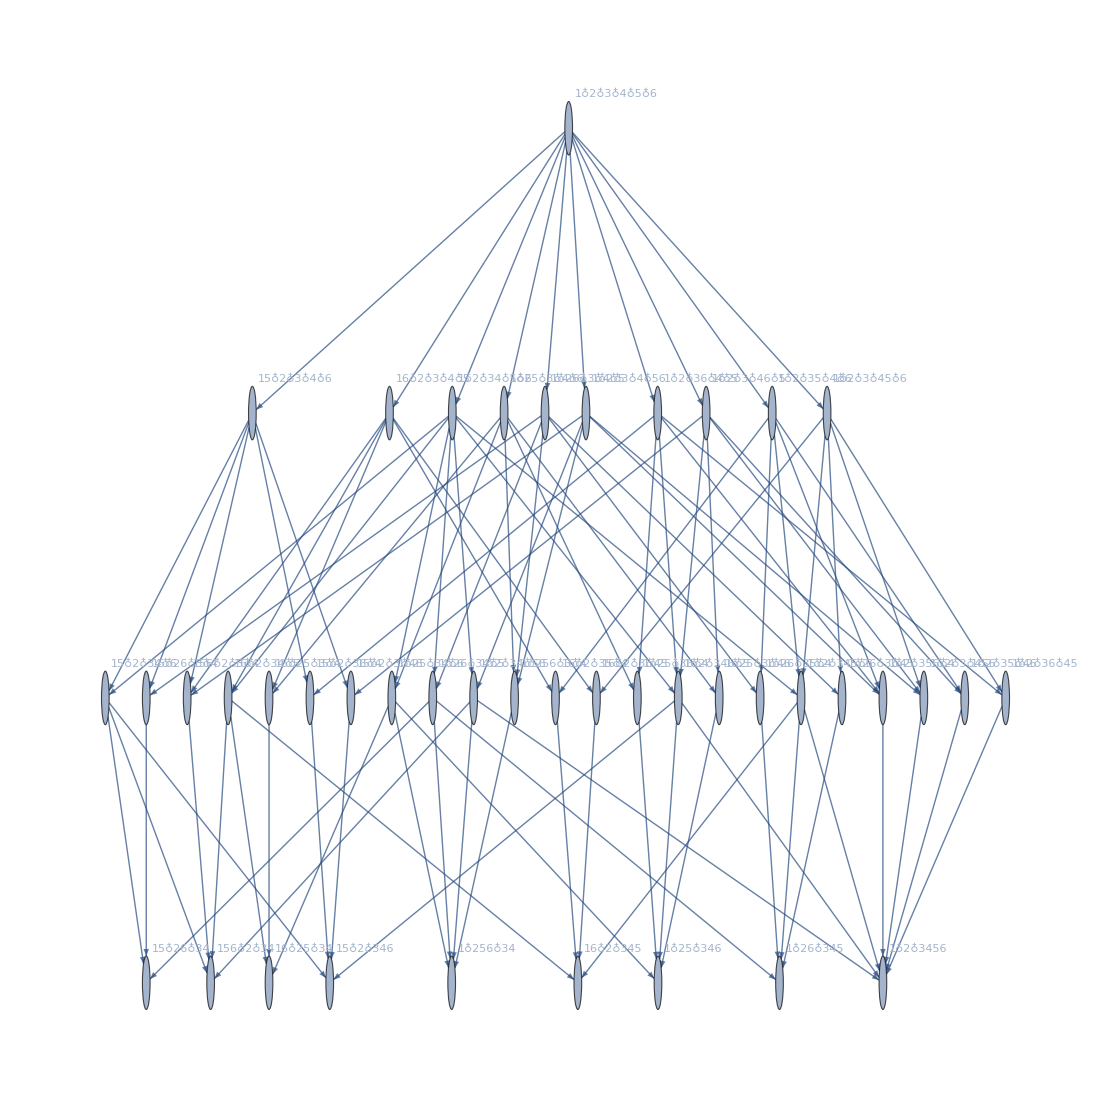

```mathematica
FormulaGraph[allGraphs6[6934977,"colofour"]]
```